```mathematica
SetDirectory[NotebookDirectory[]]


bound=75
```

D:\Cline_and_dispersal\Fat-tailed_migration_cline

75

```mathematica
tf=1000 (*max time point we have a large time to indicate equilibrium*)
```

1000

```mathematica
scoef=0.015
```

0.015

```mathematica
f1[x_]=Piecewise[{{0, x < 0},{1, x >= 0}}]        (*This function is to determine the boundary conditons for this selection landscape. The number in the function refers to the selection function number in the code*)
```

Piecewise[{{0, x<0}, {1, x≥0}, {0, True}}]

```mathematica
f2[x_]=Piecewise[{{1, x < -bound},{0, -bound<=x <=bound}, {1, x >bound}}]        (*This function is to determine the boundary conditons for this selection landscape. The number in the function refers to the selection function number in the code*)
```

Piecewise[{{1, x<-75}, {0, -75≤x≤75}, {1, x>75}, {0, True}}]

```mathematica
f3[x_]=Piecewise[{{0, x < -bound},{1, -bound<=x <=bound}, {0, x >bound}}]        (*This function is to determine the boundary conditons for this selection landscape. The number in the function refers to the selection function number in the code*)
```

Piecewise[{{0, x<-75}, {1, -75≤x≤75}, {0, True}}]

```mathematica
s1[x_]=Piecewise[{{-scoef, x < 0}, {scoef, x >0}}]
```

Piecewise[{{-0.015, x<0}, {0.015, x>0}, {0, True}}]

```mathematica
s2[x_]=Piecewise[{{scoef, x < -bound},{-scoef, -bound<=x <=bound}, {scoef, x >bound}}]
```

Piecewise[{{0.015, x<-75}, {-0.015, -75≤x≤75}, {0.015, x>75}, {0, True}}]

```mathematica
s3[x_]=Piecewise[{{-scoef, x < -bound},{scoef, -bound<=x <=bound}, {-scoef, x >bound}}]
```

Piecewise[{{-0.015, x<-75}, {0.015, -75≤x≤75}, {-0.015, x>75}, {0, True}}]

```mathematica
sigma2s=1.73
sigmaL=0.2
```

1.73

0.2

```mathematica
conv66[x_]=Piecewise[{{-1,-Infinity<x<0}, {1,Infinity>x>0}}]
```

Piecewise[{{-1, -∞<x<0}, {1, ∞>x>0}, {0, True}}]

```mathematica
equation={D[T[x,t],t]==0.5*(sigma2s)*D[T[x,t],{x,2}]+T[x,t]*(1-T[x,t])*s1[x]+(sigmaL*D[T[x,t],{x,1}])*conv66[x] 
,T[x,0]==f1[x],T[500,t]==f1[500],T[-500,t]==f1[-500]}
```

{T^(0,1)[x,t]==(Piecewise[{{-0.015, x<0}, {0.015, x>0}, {0, True}}]) (1-T[x,t]) T[x,t]+0.2 (Piecewise[{{-1, -∞<x<0}, {1, ∞>x>0}, {0, True}}]) T^(1,0)[x,t]+0.865 T^(2,0)[x,t],T[x,0]==(Piecewise[{{0, x<0}, {1, x≥0}, {0, True}}]),T[500,t]==1,T[-500,t]==0}

```mathematica
soln=NDSolve[equation,T[x,t],{t,0,tf},{x,0,500}, Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", MaxPoints->1000}}]
```

NDSolve::mxsst: Using maximum number of grid points 1000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{T[x,t]→InterpolatingFunction[{{-500., 500.}, {0., 1000.}}, <>][x,t]}}

```mathematica
stream=OpenWrite["filename.txt"]; (*Open a file for writing*)
For[i=-500,i<=500,i++,q=(T[x, t] /. soln) /. t -> tf /. x -> i ;m=ToString[AccountingForm[q[[1]]]];statement=ToString[i] <>","<> m<>"\n";WriteString[stream,statement]; ]
Close[stream]; (*Close the file*)
```

C:\Users\Sherif\Documents

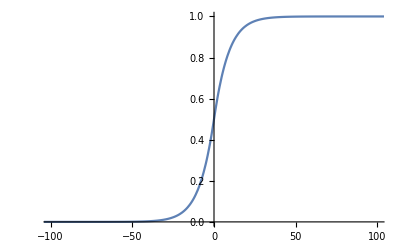

```mathematica
Plot[(T[x,t]/. soln)/. t->tf,{x,-500,500},PlotRange->{{-100,100},{0,1}}]
```